```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 283 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
Clear[constraint]
constraint = 
( R - r ) θ[t] == r ϕ[t]
```

(-r+R) θ[t]==r ϕ[t]

```mathematica
D[constraint, t]
```

(-r+R) θ'[t]==r ϕ'[t]

```mathematica
Clear[ϕtReplace]
ϕtReplace = 
Flatten[Solve[ D[constraint, t] , ϕ'[t] ]]
```

{ϕ'[t]→-((r-R) θ'[t])/r}

```mathematica
Clear[s]
s = { ( R - r ) Sin[θ[t]] , - ( R -r ) Cos[θ[t]] }
```

{(-r+R) Sin[θ[t]],(r-R) Cos[θ[t]]}

```mathematica
D[s, t]
```

{(-r+R) Cos[θ[t]] θ'[t],-(r-R) Sin[θ[t]] θ'[t]}

```mathematica
D[s, t] . D[s, t]
```

(-r+R)^2 Cos[θ[t]]^2 θ'[t]^2+(r-R)^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand
```

r^2 Cos[θ[t]]^2 θ'[t]^2-2 r R Cos[θ[t]]^2 θ'[t]^2+R^2 Cos[θ[t]]^2 θ'[t]^2+r^2 Sin[θ[t]]^2 θ'[t]^2-2 r R Sin[θ[t]]^2 θ'[t]^2+R^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand  // Simplify
```

(r-R)^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[s, t] . D[s, t]  // Expand  // Simplify  ) + 1/2( 1/2 m r^2) ϕ'[t]^2
```

1/2 m (r-R)^2 θ'[t]^2+1/4 m r^2 ϕ'[t]^2

```mathematica
Clear[V]
V = - m g ( R - r ) Cos[θ[t]]
```

-g m (-r+R) Cos[θ[t]]

```mathematica
T - V 
Clear[ℒ]
ℒ = T - V  /. ϕtReplace
```

g m (-r+R) Cos[θ[t]]+1/2 m (r-R)^2 θ'[t]^2+1/4 m r^2 ϕ'[t]^2

g m (-r+R) Cos[θ[t]]+3/4 m (r-R)^2 θ'[t]^2

```mathematica
Clear[q]
q = θ[t]
```

θ[t]

```mathematica
Simplify[D[ D[ ℒ , D[q, t] ], t ] - D[ ℒ , q ]== 0   ]
```

m (r-R) (-2 g Sin[θ[t]]+3 (r-R) θ''[t])==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

1/2 m (r-R) (2 g Sin[θ[t]]-3 (r-R) θ''[t])==0

```mathematica
Normal[Series[ Sin[θ[t]] , { θ[t] , 0, 1 } ]]
```

θ[t]

```mathematica
Clear[linearized]
linearized = 
eqs /. Sin[θ[t]] -> Normal[Series[ Sin[θ[t]] , { θ[t] , 0, 1 } ]]
```

1/2 m (r-R) (2 g θ[t]-3 (r-R) θ''[t])==0

```mathematica
eqs
linearized
```

1/2 m (r-R) (2 g Sin[θ[t]]-3 (r-R) θ''[t])==0

1/2 m (r-R) (2 g θ[t]-3 (r-R) θ''[t])==0

```mathematica
Clear[parameters]
parameters =  { 
R -> 10 , 
r -> 2 ,
m -> 3 , 
g -> 9.8 
} ;
parameters // TableForm
```

R→10
r→2
m→3
g→9.8

```mathematica
eqs /. parameters 
linearized /. parameters
```

-12 (19.6 Sin[θ[t]]+24 θ''[t])==0

-12 (19.6 θ[t]+24 θ''[t])==0

```mathematica
Clear[ics]
ics = { 
θ[0] == π/4 ,
θ'[0] == 0 
} ;
ics // TableForm
```

θ[0]==π/4
θ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[{  eqs /. parameters }  , ics ] , q, { t, 0, 100 } ] ]
```

{θ[t]→InterpolatingFunction[…][t]}

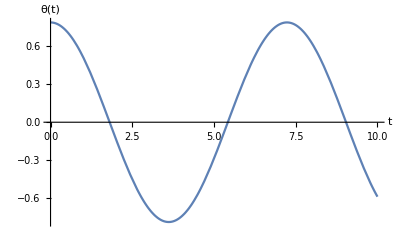

```mathematica
Plot[ Evaluate[ q /. solution[t] ], { t, 0, 10 } , AxesLabel-> { t , q  } ]
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{θ[t]→InterpolatingFunction[…][t]}

θ[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[
ParametricPlot[ {  solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax }  , AxesLabel-> { q , D[q, t] } ]  , { tmax , 0.1 , 20 } ]
```

```mathematica
eqs
linearized
```

1/2 m (r-R) (2 g Sin[θ[t]]-3 (r-R) θ''[t])==0

1/2 m (r-R) (2 g θ[t]-3 (r-R) θ''[t])==0

```mathematica
Flatten[Solve[ linearized , θ''[t]]]
```

{θ''[t]→(2 g θ[t])/(3 (r-R))}

```mathematica
Clear[ω]
ω = 
Sqrt[Coefficient[Flatten[Solve[ linearized , θ''[t]]][[1,2]] , θ[t]]]
```

√(2/3) √(g/(r-R))

```mathematica
(2 π)/ω // PowerExpand
```

(√6 π √(r-R))/(√g)